# Homework 12

## Exercise 1

f(x) = 3x + 5
Δf(x)=(f(x_0+h) - f(x_0))/(x_0+h - x_0)=(3(x_0+ h) + 5 - [3(x_0) + 5])/h=(3 x_0+3h +5 -3 x_0- 5)/h=(3h)/h=3
∴ strictly positive

f(x) = -2x + 5
Δf(x) = (f(x_0+h) - f(x_0))/(x_0+h - x_0)=(-2(x_0+ h) + 5 - [-2(x_0) + 5])/h=(-2 x_0-2h+5+2 x_0-5)/h=(-2h)/h=-2
∴ strictly decreasing

f(x) = x^2
Δf(x) = (f(x_0+h) - f(x_0))/(x_0+h - x_0)=((x_0+ h)^2-x_0^2)/h=(x_0^2+2h x_0+h^2 -x_0^2)/h=(h(2 x_0+h))/h=2 x_0 + h
∴ Not strictly monotone

f(x) = x^3
Δf(x) = (f(x_0+h) - f(x_0))/(x_0+h - x_0)=((x_0+ h)^3-x_0^3)/h=((x_0^2+2h x_0+h^2 )(x_0+h)-x_0^2)/h=(x_0^3+3h x_0^2+3 h^2 x_0+h^3 -x_0^3)/h=3 x_0^2+3h x_0+h^2
∴ Not strictly monotone

## Exercise 2

x ↦ abs(x)
From the left: (abs(-1) - abs(0))/(-1 - 0) = -1
From the right: (abs(1) - abs(0))/(1 - 0) = 1
Therefore, it must be the case that the slope is 0 at some point in between.  Thus 0 must be an extrema or inflection point.  Since the slope is negative on the left and positive on the right abs(0) is a minimum.

x ↦ x^2
From the left: ((-1)^2 - 0^2)/(-1 - 0) = -1
From the right: (1^2 - 0)/(1 - 0) = 1

Therefore, it must be the case that the slope is 0 at some point in between.  Thus 0 must be an extrema or inflection point.  Since the slope is negative on the left and positive on the right abs(0) is a minimum.

x ↦ x^3
From the left: ((-1)^3 - 0^3)/(-1 - 0) = 1
From the right: (1^3 - 0)/(1 - 0) = 1

The slope is positive on both sides of the point, so 0 is neither maximizes nor minimizes the function.

x ↦ x^4
From the left: ((-1)^4-0^2)/(-1-0) = -1
From the right: (1^4-0)/(1-0) = 1

Therefore, it must be the case that the slope is 0 at some point in between.  Thus 0 must be an extrema or inflection point.  Since the slope is negative on the left and positive on the right abs(0) is a minimum.

We can use the second derivative test for each case except for the functions x ↦ abs(x) because the function is not differentiable at x = 0 and x↦x^3 and x↦x^4 because the second derivative is 0 there.

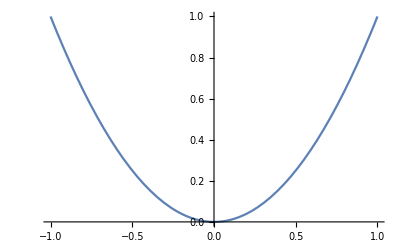

```mathematica
Plot[x^2, {x, -1, 1}]
```

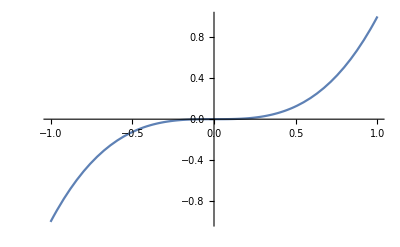

```mathematica
Plot[x^3, {x, -1, 1}]
```

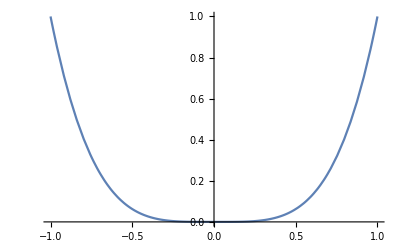

```mathematica
Plot[x^4, {x, -1, 1}]
```

## Exercise 3

A function is concave if ∀_(t ∈ [0, 1]) f((1-t)x+t(y))≥(1-t)f(x)+tf(y).  That is, for any f:ℝ↦ℝ, the point (z,f(z)) (where z is in the interval between x and y) is always above the endpoints (x, f(x)) and (y, f(y)) of the interval.

Jensen’s inequality states that for a concave function f:ℝ↦ℝ and positive numbers p_1 ... p_n that sum to 1, we have f(∑_(i=1)^n p_i x_i)≥∑_(i=1)^n p_i f(x_i).

Proof
Base Case
Consider two points on the domain of the function x_1 and x_2, where x_1 < x_2, and two weights p_1 and p_2.  Since we have the requirement that p_1 + p_2 = 1, it must be that p_2 = 1-p_1.
For the concave function we have:
f(p_1 x_1 + (1-p_1) x_2) ≥ p_1 f(x_1)+(1-p_1)f(x_2) (definition of concavity)
Inductive Case
Consider the case of the points x_1 ... x_(n-1) and x_n (with x_(n-1) < x_n), and weights p_1 ... p_(n-1), p_n.  We require that the sum of the weights p_1, ... p_n is 1, so it must be the case that p_n = 1 - ∑_(i=1)^n  p_(n-1).

We assume that
f(∑_(i=1)^(n-1) p_i x_i)≥∑_(i=1)^(n-1) p_i f(x_i).
We rewrite f(∑_(i=1)^n p_i x_i) = f(p_n x_n + (1-p_n) ∑_(i=1)^(n-1) p_i/(1 - p_n)x_i).  Since, ∑_(i=1)^(n-1) p_i/(1 - p_n) = 1, we can say:
f(p_n x_n + (1-p_n) ∑_(i=1)^(n-1) p_i/(1 - p_n)x_i) ≥ p_n f(x_n) + (1-p_n) f(∑_(i=1)^(n-1) p_i/(1 - p_n)x_i) by definition of concavity.  We can rewrite the above sums (i.e. slide the p_n x_n term back into the sum) to obtain:
  f(∑_(i=1)^n p_i x_i)≥∑_(i=1)^n p_i f(x_i) which is Jensen’s inequality.

## Exercise 4

Prove f(x) = x^2 is convex.

Is ((1 - t) x + t y)^2 ≤ (1 - t) x^2 + t y^2
((1 - t) x + t y)^2 = ((x - t x) + t y)^2 = (x - t x + t y)^2 = x^2-2 t x^2+t^2 x^2+2 t x y-2 t^2 x y+t^2 y^2
(1 - t(2 + t)) x^2 + t^2 y^2 + 2 x y (t - t^2).

Note that (1 - t(2 + t)) takes the maximum value between 1 and -2, thus (1 - t(2 + t)) x^2 ≤ (1-t)x^2.
Also, t^2 ≤ t, thus t^2 y ≤ t y.  Thus we have (1 - t(2 + t)) x^2 + t^2 y^2 ≤ (1 - t) x^2 + t y^2.  However, we are still missing the piece 2 x y (t - t^2) on the left hand side from the expansion of ((1 - t) x + t y)^2.  We can rewrite this as 2 x y t(1-t) or 2(1-t)x t y.  This term takes on a maximum value at t = 0.5

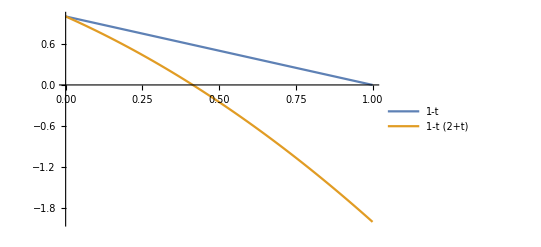

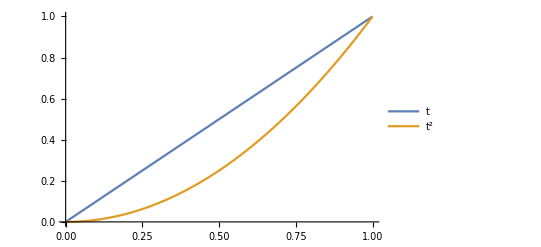

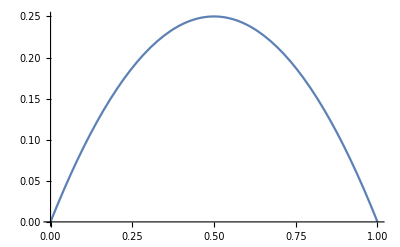

```mathematica
Plot[{(1-t), (1-t(2+t))}, {t, 0, 1}, PlotLegends->"Expressions"]
Plot[{t, t^2}, {t, 0, 1}, PlotLegends->"Expressions"]
Plot[t-t^2, {t, 0, 1}, PlotLegends->"Expressions"]
```

## Exercise 5

5.11
a) PV = 215/e^(0.1*2) = 176.03
b) PV = 100/e^(0.1*1) + 100/e^(0.1*2) = 172.36
c) PV = 100 + 95/e^(0.1*2) = 177.78

Option C has the highest PV

5.12
a) 500/e^(.1*1) + 500/e^(.1*2) +500/e^(.1*3) +500/e^(.1*4) +500/e^(.1*5) = 1870.62
b) 500 ∑_(n = 1)^∞  1/e^(.1n) = 500 1/(e^(-1/10)- 1)=4754.17
5.13
B(t) = 2 √t
ln B(t)  = ln 2 √t
B'(t) = ln 2
(B'(t))/(B(t)) = (ln 2)/(2 √t) = 0.05
t = 48.05

5.14
ln V(t) = K + √t
V’/V = 1/2 √t = r
t  = 1/(4 r^2)

5.15
ln V(t) = ln 2000 + t^(1/4)
V'/V= 1/4 t^(-3/4) = r
t = (4r)^(-4/3)
r = 0.1  --> t = 3.39

5.16
a) ln f(x) = 1/2ln(x^2+1) - 1/2 ln(x^2+4)
f'/f = x/(x^2+1) - x/(x^2 + 4)
f’(x) = (3x)/((x^2+1)^(1/2)(x^2+4)^(3/2))

b) ln f(x) = 2 x^2 ln x
f'/f = 4x ln x 1 2x = 2x(1 + ln x^2)
f’(x) = 2x(1 + ln x^2) (x^2)^(x^2)

5.17
h(x) = f(x)g(x)
ln h = ln f + ln g
h'/h = f'/f + g'/g
x h'/h = x(f'/f+g'/g)

## Exercise 6

c = 0.1π
t_s = 0.05(π - c)
t_f = 0.4(π - c - t_s)

Uknownks are c, t_s and t_f
1 c + 0 t_s + 0 t_f = 0.1 π
0.05 c + 1 t_s + 0 t_f = 0.05π
0.4 c - 0.4 t_s + 1 t_f = 0.4π

In Matrix Form
(1 | 0 | 0 | 10000
5/100 | 1 | 0 | 5000
4/10 | 4/10 | 1 | 40000)

or we can rewrite as
(1 | 4/10 | 4/10 | 40000
0 | 1 | 5/100 | 5000
0 | 0 | 1 | 10000)

subtract 5/100 R_3 from R_2
(1 | 4/10 | 4/10 | 40000
0 | 1 | 0 | 4500
0 | 0 | 1 | 10000)

subtract 4/10 R_2 from R_1
(1 | 0 | 4/10 | 38200
0 | 1 | 0 | 4500
0 | 0 | 1 | 10000)

subtract 4/10 R_3 from R_1
(1 | 0 | 0 | 34200
0 | 1 | 0 | 4500
0 | 0 | 1 | 10000)

c = 10000
t_s = 4500
t_f = 34200

If the state now allows federal taxes to be deducted, we have
c = 0.1π
t_s = 0.05(π - c - t_f) = 0.05π - 0.05c -0.05 t_f
t_f = 0.4(π - c - t_s)

Or in Matrix form:

(1 | 0 | 0 | 10000
5/100 | 1 | 5/100 | 5000
4/10 | 4/10 | 1 | 40000)

If we row reduce this, we obtain
(1. | 0. | 0. | 10000.
0. | 1. | 0. | 2755.1
0. | 0. | 1. | 34898.)
Or
c = 10000
t_s = 2755.10
t_f = 34898.10

```mathematica
eq = {{1, 0, 0, 10000}, {5/100, 1, 0, 5000}, {4/10, 4/10, 1, 40000}}
%//MatrixForm
RowReduce[eq]//MatrixForm
```

{{1,0,0,10000},{1/20,1,0,5000},{2/5,2/5,1,40000}}

(1 | 0 | 0 | 10000
1/20 | 1 | 0 | 5000
2/5 | 2/5 | 1 | 40000)

(1 | 0 | 0 | 10000
0 | 1 | 0 | 4500
0 | 0 | 1 | 34200)

```mathematica
eq2 = {{1, 0, 0, 10000}, {5/100, 1, 5/100, 5000}, {4/10, 4/10, 1, 40000}}
%//MatrixForm
RowReduce[eq2]//MatrixForm
```

{{1,0,0,10000},{1/20,1,1/20,5000},{2/5,2/5,1,40000}}

(1 | 0 | 0 | 10000
1/20 | 1 | 1/20 | 5000
2/5 | 2/5 | 1 | 40000)

(1 | 0 | 0 | 10000
0 | 1 | 0 | 135000/49
0 | 0 | 1 | 1710000/49)

### Exercise 7

C = cD
R = rD
H = C + R
M = C + D

Unknowns M, D, R, C
1 M + -1 D + 0 R + -1 C = 0
0 M + 0 D + 1 R + 1 C = H
0 M + -r D + 1 R + 0 C = 0
0 M + -c D + 0 R + 1 C = 0

or in matrix form
(1 | -1 | 0 | -1 | 0
0 | 0 | 1 | 1 | H
0 | -r | 1 | 0 | 0
0 | -c | 0 | 1 | 0)

After row reduction we obtain:
(1 | 0 | 0 | 0 | (h+c h)/(c+r)
0 | 1 | 0 | 0 | h/(c+r)
0 | 0 | 1 | 0 | (h r)/(c+r)
0 | 0 | 0 | 1 | (c h)/(c+r))
or:
M = (H + cH)/(C + R)
D = H/(C + R)
R = (H R)/(C+R)
C = (C H)/(C+R)

```mathematica
eq = {{1, -1, 0, -1, 0}, {0, 0, 1, 1, h}, {0, -r, 1, 0, 0}, {0, -c, 0, 1, 0}}
eq // MatrixForm
RowReduce[eq]//MatrixForm
```

{{1,-1,0,-1,0},{0,0,1,1,h},{0,-r,1,0,0},{0,-c,0,1,0}}

(1 | -1 | 0 | -1 | 0
0 | 0 | 1 | 1 | h
0 | -r | 1 | 0 | 0
0 | -c | 0 | 1 | 0)

(1 | 0 | 0 | 0 | (h+c h)/(c+r)
0 | 1 | 0 | 0 | h/(c+r)
0 | 0 | 1 | 0 | (h r)/(c+r)
0 | 0 | 0 | 1 | (c h)/(c+r))

## Exercise 8

a) Augmented Matrix:
(1 | 2 | 5
3 | 4 | 6)

R_2 - 3 R_1
(1 | 2 | 5
0 | -2 | -9)

-1/2 R_2
(1 | 2 | 5
0 | 1 | 9/2)

R_1 - 2 R_2
(1 | 0 | -4
0 | 1 | 9/2)
x = (-4
9/2)

b) 
(1 | 2 | 7
3 | 4 | 8) → (1 | 2 | 7
0 | -2 | -13) → (1 | 2 | 7
0 | 1 | -13/2) →(1 | 0 | -6
0 | 1 | -13/6)
x = (-6
13/2)
c) 
(1 | 2 | 9
3 | 4 | 10) → (1 | 2 | 9
0 | -2 | -17) →  (1 | 2 | 9
0 | 1 | 17/2) →  (1 | 0 | -8
0 | 1 | 17/2) 
x=(-8
17/2)

d)
(1 | 2 | 3 | 4
2 | 2 | 3 | 5
3 | 1 | 3 | 6) → (1 | 2 | 3 | 4
0 | -2 | -3 | -3
0 | -5 | -6 | -6) → (1 | 0 | 0 | 1
0 | 1 | 3/2 | 3/2
0 | 0 | 3/2 | 3/2) → (1 | 0 | 0 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 1)
x = (1
0
1)

## Exercise 9

(I-A)^2 = (I-A) (I-A)
I^2 - IA - AI + A^2 (matrix multiplication is distributive)
but IA = AI = A (mutiplying by the identity is commutative)
and I^2 = I (identity matrix is idempotent)
∴ I - A - A + A^2
but A is idempotent so A^2 = A
∴ (I - A)^2 = I - A

A^2 = AA
 I - A^2 =  (I - A) (I - A) = (I-A)^2
 but (I-A)^2 = (I-A)
 ∴ A^2 = A

## Exercise 10

a) The diemensions of A^T is K×R.
b) A^TA has diemnsions K×K. (A^T A)^-1 also has diemnsions K×K. (A(A^T A))^-1 has diemnsions R×K. (A(A^T A))^-1 A^T has diemnsions K×K.  Therefore M = I − A (A^T A)^(−1)A^T has diemnsions K×K

## Exercise 11

ABC = (AB)C
For the matrix AB the element e_rc in the r^th row and c^th column is given as
A_r B_c^T  where A_r is the r^th row of matrix A and B_c is the c^th column of matrix B.

Then for e_(2,1) we have [3, 4] [5
7] = 15 + 28 = 43
Similarly for e_(2, 2) we have [3, 4] [6
8] = 50

For the e_(2, 1) element of the matrix ABC, we will have
AB_2 C_1 = [43, 50] [9
11] = 937

```mathematica
{{1, 2}, {3, 4}}.{{5, 6},{7, 8}}.{{9, 10},{11, 12}}//MatrixForm
```

(413 | 454
937 | 1030)

## Exercise 12

A A^-1 = A^-1 A = I (def of inverse)
I^T = I (identity matrix is symmetric)
(A A^-1)^T = AA^-1 (identity matrix is symmetric)
(A A^-1)^T = (A^-1)^T A^T (law of product of transpose)
A^-1 A = (A^-1)^T A^T (using A^-1 A = AA^-1=I)
A^-1 A = (A^-1)^T A (using A^T = A)
A^-1 (A A^-1) = (A^-1)^T (A A^-1) (post-multiply by A^-1)
A^-1 I = (A^-1)^T I
A^-1 = (A^-1)^T

## Exercise 13

A = [1 | -1
0 | 4]
|A - λI| = |[1 | -1
0 | 4] - [λ | 0
0 | λ]| = 0
|[1-λ | -1
0 | 4-λ]| = 0
(1-λ) (4-λ) + 1 = 0
4 - λ -4λ + λ^2 = 0
λ^2 - 5λ + 4 = 0
λ = (5 ± √(25 - 16))/2 = {4, 1}

B = [3 | 2
1 | 2] →|3-λ | 2
1 | 2-λ| = 0 → (3-λ)(2-λ) - 2 = 0 → 6 - 3λ -2λ + λ^2 - 2 = λ^2 - 5λ -4
λ = {1, 4}

C = [8 | 0
-3 | 2] → |8-λ | 0
-3 | 2-λ| = 0 → (8-λ)(2-λ) = 0
λ = {8, 2}

```mathematica
Eigenvalues[{{3, 2}, {1, 2}}]
Eigenvalues[{{8, 0}, {-3, 2}}]
```

{4,1}

{8,2}